```mathematica
vPrior[θ_,α_,β_]:= PDF[BetaDistribution[α,β],θ]
vLikelihood[θ_,nSampleSize_Integer,nDiseased_Integer]:=Likelihood[BinomialDistribution[nSampleSize,θ],{nDiseased}]
vPosterior[θ_,nSampleSize_Integer,nDiseased_Integer,α_,β_]:= PDF[BetaDistribution[α+nDiseased,β + nSampleSize-nDiseased],θ]
fShowPriorLikelihoodPosterior[α_,β_,nSampleSize_Integer,nDiseased_Integer]:=Module[{},Show[GraphicsColumn[{Plot[vPrior[θ,α,β],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf"},PlotLabel->"prior",PlotStyle->Blue,PlotRange->Full],Plot[vLikelihood[θ,nSampleSize,nDiseased],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","likelihood"},PlotStyle->Blue,PlotLabel->"likelihood"],Plot[vPosterior[θ,nSampleSize,nDiseased,α,β],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","pdf"},PlotStyle->Blue,PlotLabel->"posterior"]}],ImageSize->400]]
```

```mathematica
Manipulate[fShowPriorLikelihoodPosterior[α,β,nSampleSize,nDiseased],Style["Prior parameters",Bold,Medium],{{α,1,"Beta 1"},1,10,1},{{β,1,"Beta 2"},1,10,1},Delimiter,Style["Data",Bold,Medium],{{nSampleSize,10,"Sample size"},10,100,1},{{nDiseased,1,"number with disease"},1,nSampleSize,1},ControlPlacement->Left]
```

```mathematica
CloudDeploy[Manipulate[fShowPriorLikelihoodPosterior[α,β,nSampleSize,nDiseased],Style["Prior parameters",Bold,Medium],{{α,1,"Beta 1"},1,10,1},{{β,1,"Beta 2"},1,10,1},Delimiter,Style["Data",Bold,Medium],{{nSampleSize,10,"Sample size"},10,100,1},{{nDiseased,1,"number with disease"},1,nSampleSize,1},ControlPlacement->Left],Permissions->"Public"]
```

$Aborted

```mathematica
g1=Manipulate[Module[{},Show[GraphicsColumn[{Plot[PDF[BetaDistribution[α,β],θ],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf"},PlotLabel->"prior",PlotStyle->Blue,PlotRange->Full],Plot[Likelihood[BinomialDistribution[nSampleSize,θ],{nDiseased}],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","likelihood"},PlotStyle->Blue,PlotLabel->"likelihood"],Plot[PDF[BetaDistribution[α+nDiseased,β + nSampleSize-nDiseased],θ],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","pdf"},PlotStyle->Blue,PlotLabel->"posterior"]}],ImageSize->400]],Style["Prior parameters",Bold,Medium],{{α,1,"Beta 1"},1,10,1},{{β,1,"Beta 2"},1,10,1},Delimiter,Style["Data",Bold,Medium],{{nSampleSize,10,"Sample size"},10,100,1},{{nDiseased,1,"number with disease"},1,nSampleSize,1},ControlPlacement->Left]
```

```mathematica
g1=Manipulate[Plot[PDF[BetaDistribution[a,b],x],{x,0,1}],{a,1,10,1},{b,1,10,1}]
```

```mathematica
CloudDeploy[g1]
```

CloudObject[]

```mathematica
aList=Outer[List,Range[10],Range[10]]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}}

```mathematica
Table[ArrayReshape[PDF[BetaDistribution[#1,#2],i]&@@@(Flatten[aList,1]),{10,10}],{i,0,1,0.1}]
```

```mathematica
aResults=Table[{{a,b},Table[{θ,PDF[BetaDistribution[a,b],θ]},{θ,0.01,0.99,0.01}]},{a,1,10,1},{b,1,10,1}];
```

```mathematica
g1=Manipulate[ListLinePlot@aResults[[a,b,2]],{a,1,10,1},{b,1,10,1}]
```

```mathematica
CloudDeploy[g1,Permissions->"Public"]
```

CloudObject[]

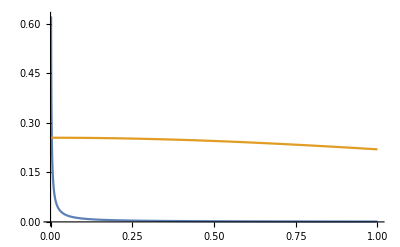

```mathematica
Plot[{PDF[GammaDistribution[0.001,1/0.001],x],2*PDF[CauchyDistribution[0,2.5],x]},{x,0,1}]
```